Consider a solar coronal plasma with ρ = 5×10^-13 kg m^-3. Assume a particular length scale, L, and compute the thermal conduction time scale, τ_(cond.), and the radiation time scale, τ_(rad.), for the temperature varying in the interval 10^4 K < T < 10^7K. Discuss the results and the relative importance of conduction and radiation depending on the assumed length scale. Use κ_(||)= 10^-11T^(5/2) Wm^-1K^-1, μ̃ = 0.6, and Hildner’s parameters for the optically-thin cooling function, namely

```mathematica
τcond=Simplify[(γ p L^(2))/((γ-1)κparal T)] ;(*From the pdf file attached with this code*)
τrad=Simplify[(γ p)/((γ-1) ρ^(2) χast T^(α))] ;(*From the pdf file attached with this code*)
Print["(τ_(rad.))/(τ_(cond.)) = ",Simplify[τrad/τcond]](*For the discussion of the results*)
```

(τ_(rad.))/(τ_(cond.)) = (T^(1-α) κparal)/(L^2 ρ^2 χast)

```mathematica
ρ=5 10^(-13);
tildeμ=0.6;
γ=5/3;(*From the pdf file attached with this code*)
R=8314.;(*Ideal gas constant (Units: kg m^2 s^-2 K^-1 mol^-1)*)
L=10^(8);(*Typical coronal loop length scale (Units: m). From the pdf file attached with this code*)
τcondlist={};
τradlist={};
relτradτcondlist={};(*For the results of (τ_(rad.))/(τ_(cond.))*)
Tlist1=Range[10^4,8 10^4,10^3];
Tlist2=Range[8 10^4+10^3,3 10^5,10^3];
Tlist3=Range[3 10^5+10^3,8 10^5,10^3];
Tlist4=Range[8 10^5+10^4,10^7,10^4];
```

```mathematica
Do[κparal=10^(-11) T^(5/2);χast=4.29 10^(10);α=1.8;p=ρ R T/tildeμ(*From the pdf file attached with this code*);AppendTo[τcondlist,{T,Simplify[(γ p L^(2))/((γ-1)κparal T)] }];AppendTo[τradlist,{T,Simplify[(γ p)/((γ-1) ρ^(2) χast T^(α))] }];AppendTo[relτradτcondlist,{T,Simplify[(κparal T^(1-α))/(L^(2) ρ^(2) χast)]}],{T,Tlist1}];
Do[κparal=10^(-11) T^(5/2);χast=2.86 10^(19);α=0;p=ρ R T/tildeμ(*From the pdf file attached with this code*);AppendTo[τcondlist,{T,Simplify[(γ p L^(2))/((γ-1)κparal T)] }];AppendTo[τradlist,{T,Simplify[(γ p)/((γ-1) ρ^(2) χast T^(α))] }];AppendTo[relτradτcondlist,{T,Simplify[(κparal T^(1-α))/(L^(2) ρ^(2) χast)]}],{T,Tlist2}];
Do[κparal=10^(-11) T^(5/2);χast=1.41 10^(33);α=-2.5;p=ρ R T/tildeμ(*From the pdf file attached with this code*);AppendTo[τcondlist,{T,Simplify[(γ p L^(2))/((γ-1)κparal T)] }];AppendTo[τradlist,{T,Simplify[(γ p)/((γ-1) ρ^(2) χast T^(α))] }];AppendTo[relτradτcondlist,{T,Simplify[(κparal T^(1-α))/(L^(2) ρ^(2) χast)]}],{T,Tlist3}];
Do[κparal=10^(-11) T^(5/2);χast=1.97 10^(24);α=-1.0;p=ρ R T/tildeμ(*From the pdf file attached with this code*);AppendTo[τcondlist,{T,Simplify[(γ p L^(2))/((γ-1)κparal T)] }];AppendTo[τradlist,{T,Simplify[(γ p)/((γ-1) ρ^(2) χast T^(α))] }];AppendTo[relτradτcondlist,{T,Simplify[(κparal T^(1-α))/(L^(2) ρ^(2) χast)]}],{T,Tlist4}];
```

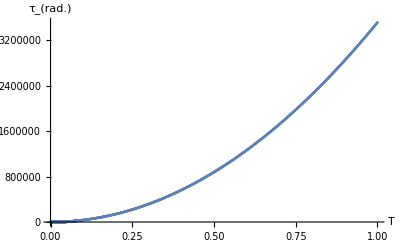

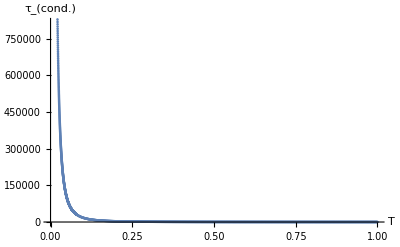

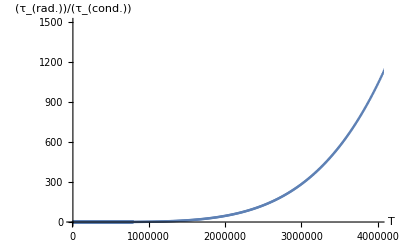

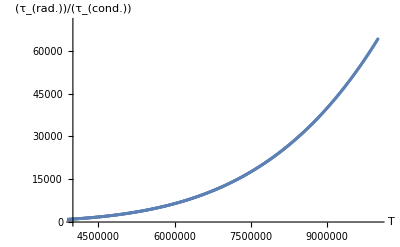

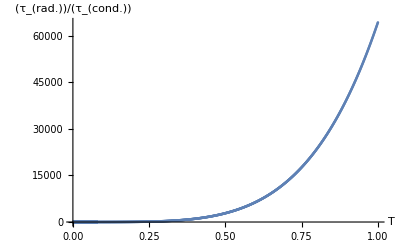

```mathematica
ListPlot[τradlist,AxesLabel->{T,"τ_(rad.)"}]
ListPlot[τcondlist,AxesLabel->{T,"τ_(cond.)"}]
ListPlot[relτradτcondlist,AxesLabel->{T,"(τ_(rad.))/(τ_(cond.))"},PlotRange->{{10^4,4 10^6},{0,1500}}]
ListPlot[relτradτcondlist,AxesLabel->{T,"(τ_(rad.))/(τ_(cond.))"},PlotRange->{{4 10^6,10^7},{0,70000}}]
ListPlot[relτradτcondlist,AxesLabel->{T,"(τ_(rad.))/(τ_(cond.))"},PlotRange->All]
```

As can be seen in the graphs, on typical coronal loop length scales L ∼ 10^8 m, τ_(rad.) increases polynomially and significantly quickly as T grows, clearly dominating solar corona plasma processes with similar or larger time scales at generally low coronal temperatures (∼ ≤ 9.4×10^5 K), while τ_(cond.) decreases also polynomially and rapidly with T, heavily influencing the dynamics with comparable or higher time scales at common/high coronal temperatures (∼ ≥ 9.4×10^5 K). Thus, in summary, for solar coronal plasma processes with similar or larger time scales, the solar coronal physics is more significantly affected by radiation at relatively low coronal temperatures and by thermal conduction at typical and high coronal temperatures; however both are substantially present and actively play a role in the solar corona, although thermal conduction is considered more important. 

Additionally, as only τ_(cond.) depends on the length scale L (specifically, in a constant factor of L^2), as the assumed length scale increases, thermal conduction loses relevance at low coronal temperatures and, consequently, radiation plays an even bigger role in this temperature range; conversely, the opposite behavior occurs when the assumed length scale decreases.